InterpolatingFunction[{{0., 20.}}, <>]

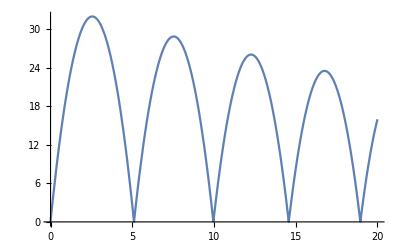

```mathematica
Needs["VariationalMethods`"]
ClearAll["Global`*"];
pars={m->1,g->9.8};
T[t_]=1/2 m y'[t]^2;
V[t_]=m g y[t];
L[t_]=T[t]-V[t];
eqn=EulerEquations[L[t],y[t],t];
soln=NDSolveValue[{eqn/.pars,y[0]==0.1,y'[0]==25, WhenEvent[y[t]==0,y'[t]->-0.95y'[t]]},y,{t,0,20}]
Plot[soln[t],{t,0,20}]
```